## Generating the Loop Equations

## Words, Symmetries, Bracelets and Necklaces

The general idea is that we’ve got some partition of the set of permutations of matrices; we’d like to map every element of some partition down to a single “canonical representation” of the partition, then simplify the loop equations down further.

The trace is cyclically symmetric, and symmetric under reversal.This means that every element in a bracelet has the same trace.

Therefore we can get some simplification out of the gate by mapping each sequence of matrices down to some “canonical element” of the bracelet. As long as the symbols we use have an ordering, we can simply expand some element out to its bracelet, sort and take the first element.

### Symmetry Functions

Here are some symmetries we’re interested in.

```mathematica
id[xs_] := {xs};
id::usage := "Returns a singleton list of the input. An ID symmetry, if you will.";

paired[rules__] := Module[{f, m=Association[{rules}]},
f[xs_] := 
DeleteDuplicates @ {xs, Lookup[m, #, #]& /@ xs};
f
];
paired::usage = "Returns a symmetry generator that swaps reflected elements.";

cycles[{}] := {{}};
cycles[xs_] := NestList[RotateLeft,xs,Length[xs]-1];
cycles::usage = "Generates all cyclic rotations of the input list.";

reflection[xs_] := {xs, Reverse[xs]}
reflection::usage = "Generates a reflection symmetry, reversing the args.";
```

And then the ability to compose them:

```mathematica
compose[] := id;
compose[f_] := f
compose[f_, g_] := DeleteDuplicates[Join @@ g /@ f[#]] &;
compose[f_, g_, rest__] := compose[compose[f, g], rest]
compose::usage = "Composition for symmetries. Returns a new symmetry generator.";

canonical[symmetryFns__] := Module[
{f, symFn = compose @@ {symmetryFns}},
f[xs_] := First @ Sort @ symFn[xs];
f[xs__] := DeleteDuplicates[f /@ {xs}];
f
];
canonical::usage = 
"Returns a function that returns the representative element after taking all symmetries into account.";
```

Here are some common symmetries that we’re interested in:

```mathematica
necklace = cycles;
bracelet = compose[necklace, reflection];
z2Symmetry = paired["A" -> "B", "B" -> "A"];
braceletZ2 = compose[bracelet, z2Symmetry];
```

#### Tests

```mathematica
(*TODO Boom, we've recreated the bracelets. *)
VerificationTest[
bracelet[{A, B, C}],
{{A,B,C},{C,B,A},{B,C,A},{A,C,B},{C,A,B},{B,A,C}}
]

(*And necklaces... *)
VerificationTest[
necklace[{A, B, C}],
{{A,B,C},{B,C,A},{C,A,B}}]

(*And Z2 symmetry.*)
VerificationTest[
paired[A -> B,B -> A,  1 -> 2, 2 -> 1][{1,1,A, 2,1}],
 {{1, 1, A, 2, 1 }, {2,2,B, 1, 2}}]

(* If we pass lots of items, we get back the set of canonical elements. *)
VerificationTest[
canonical[necklace] @@ necklace[Range[5]],
{Range[5]}
]

(* If we pass a SINGLE item to canonical's fn, we get a single item back. *)
VerificationTest[
canonical[necklace][Range[5]],
Range[5]
]

(* Test that we're left with only the canonical form, for bracelets this time. *)
VerificationTest[
canonical[bracelet] @@ bracelet[Reverse[Range[5]]],
{Range[5]}
]

(* Single element comes back if we pass one item. *)
VerificationTest[
canonical[bracelet][Reverse[Range[5]]],
Range[5]
]
```

TestResultObject[…]

TestResultObject[…]

TestResultObject[…]

«4 more identical outputs»

### Generators

Now, an actual generator that we can apply the symmetries to. You can pass the output of “words” into the function returned by “canonical” to get a list of distinct elements!

```mathematica
words[alphabetSize_Integer, wordLength_Integer] :=Module[
{nLetters = ToUpperCase[Alphabet[]][[;; alphabetSize]]},
Tuples[nLetters,wordLength]
];
words[alphabetSize_Integer, wordLength_List] :=
Join @@ (words[alphabetSize, #]&  /@ wordLength);
words::usage = "Generates all words of length k from an alphabet of n items.";
```

#### Tests

```mathematica
VerificationTest[
words[2, 2],
{{"A","A"},{"A","B"},{"B","A"},{"B","B"}}
]
```

TestResultObject[…]

## Loop Equations from a Polynomial Model

Now we get into the good stuff! First, the quadratic terms.

### Quadratic Terms

Time to chop up some blobs. Here are some utilities for generating paths through the blob.

```mathematica
otherLocations[blob_, i_Integer] := 
Module[
{positions = Position[blob, blob[[i]]], other},
Flatten[DeleteCases[positions, {i}]]
];
otherLocations::usage =
 "Takes a list of terms and a position, and returns all OTHER places that the term at position i appears.";

routes[i_Integer, exits_] := Sort@{i,#}&/@ exits;
routes::usage = "Returns a sorted list of pairs of the form {entrance_index, exit_index} 
through a blob, from i to each of the items in 'exits'.
";

sliceBlob[blob_, {start_, end_}] := sliceBlob[blob, start, end];
sliceBlob[blob_, start_, end_] :=
 Module[{l, r},
{l, r} = TakeDrop[blob, {start, end}];
{Delete[l, {{-1}, {1}}], r}
];
sliceBlob::usage = 
"Returns a pair with both halves of the blob that remain after slicing through a path from start to end.";
```

And here’s the code that actually generates the terms.

```mathematica
quadraticTerms[toCorrelator_, blob_, i_Integer]:=
Module[
{blobRoutes, product, slice, exits=otherLocations[blob, i]},

slice[route_] := sliceBlob[blob, route];
product[{l_, r_}] := toCorrelator[l] * toCorrelator[r];

If[Length[exits] ==0,
0,
blobRoutes = routes[i, exits];
Total[(product @* slice) /@ blobRoutes]
]
];
quadraticTerms::usage = "Quadratic terms, which come from splitting up the planar graph in various ways.";

quadraticTermFn[toCorrelator_] := quadraticTerms[toCorrelator, #1, #2]&;
quadraticTermFn::usage = "Curried version of quadraticTerms.";
```

### Interaction Terms

Now we can write the terms that result from interactions described by the model.

```mathematica
termReplacements[{}] = <||>;
termReplacements[term_] := Module[{distinctTails},
distinctTails[xs_] := DeleteDuplicates @ Map[Rest, xs];
 GroupBy[cycles[term], First, distinctTails]
];
termReplacements::usage = "Generates an association of element to the other spokes on its wheel.";

termReplacementFn[term_] := Lookup[termReplacements[term], #, {}] &;
termReplacementFn::usage =
 "Similar to termReplacements, but instead of returning
  an association, returns a total function that can handle defaults
  missing from the association. (If an item is missing, the function generates
  an empty list, meaning, generate no replacements.

  Returns a function from an element to the items that it could expand to. ";

extract[blob_, interaction_, i_Integer] :=  Module[{l, r},
{l, r} = TakeDrop[blob, i];
Join [Drop[l, -1], interaction,  r]
];
extract::usage = 
"extracts the i'th term of the blob xs and replaces it with the supplied interaction term.";

interaction[term_] :=  Module[{mFn, f},
mFn = termReplacementFn[term];
f[{}, i_Integer] := {{}};
f[blob_, i_Integer] :=  Module[{v = blob[[i]]},
extract[blob, #, i]& /@ mFn[v]
];
f
];
interaction::usage =
"Take a coefficient and a polynomial term, and returns
  a function of (blob, i) that produces all possible interactions.";

termExpander[{coef_, term_}, toCorrelator_] := Module[
{ret, f = interaction[term]},
ret[blob_, i_]:= (
coef * Total[toCorrelator /@ f[blob, i]]
);
ret
];
termExpander::usage = "Returns a function of blob, i that ";

interactionTermFn[pairs_, toCorrelator_] := Module[
{ret, fs},
fs = Map[termExpander[#, toCorrelator]&, pairs];
ret[blob_, i_Integer] := Simplify[Total[#[blob, i]& /@ fs]];
ret
];
interactionTermFn::usage =
 "Takes pairs of model terms and a toCorrelator fn, and returns a function of
   (blob, i) that generates all of the model's interaction terms.";
```

#### Tests

```mathematica
(* The replacement handles flattening as well. *)
VerificationTest[
extract[{"A", "B", "C", "D"}, {"F", "G"}, 2],
{"A", "F", "G", "C", "D"}
]

VerificationTest[termReplacements[{A, A, B}], <|A->{{A,B},{B,A}},B->{{A,A}}|>]

(* If there are no mappings, returns a singleton replacement list. *)
VerificationTest[termReplacementFn[{}][A], {{A}}]

(* Same if the variable isn't present. *)
VerificationTest[termReplacementFn[{A, A, B}][C], {{C}}]

(* If it is, we should get the result of a lookup. *)
VerificationTest[termReplacementFn[{A, A, B}][A], {{A, B}, {B, A}}]

(* All replacements at position 1. *)
VerificationTest[
interaction[{"A", "A", "B"}][{"A", "B", "C", "D"}, 1],
{{"A", "B", "B", "C", "D"}, {"B", "A", "B", "C", "D"}}
]

(* If a term generates no replacements, you get a singleton list with the original input. *)
VerificationTest[
interaction[{"A", "A", "B"}][{"A", "B", "C", "D"}, 3],
{{"A", "B", "C", "D"}}
]

(* Same is true of you pass an empty blob. *)
VerificationTest[
interaction[{"A", "A", "B"}][{}, 100 ],
{{}}
]

(*Works out fine if you only have a singleton... it does break if you give it an empty blob. *)
VerificationTest[
interaction[{"A", "A", "B"}][{"A"}, 1 ],
{{"A", "B"}, {"B", "A"}}
]
```

TestResultObject[…]

TestResultObject[…]

TestResultObject[…]

«6 more identical outputs»

### Correlator Functions

Here' s some code to describe correlators in a way that captures their symmetries, and turns them into proper subscripted variable entries.

```mathematica
formal[e_, {}] = 1;
formal[e_, xs_] := Subscript[e, StringJoin[xs]];
formal::usage =
 "Function that takes a list and returns a subscript of some indexed symbol; for the empty list, returns 1.";

correlator[e_] := formal[e, #] &;
correlator[e_, symmetryFns__] := formal[e, (canonical @@ {symmetryFns})[#]] &;
correlator::usage = 
"Returns a function that generates a correlator term on the supplied variable e.
  the subscript is the canonical representation, taking into account the
  the supplied symmetries.";

(* This is cheating a little, since we're baking in the first, sort fetch of the canonical element. *)
distinctBy[toCorrelator_, words_] := 
 Values @ GroupBy[words, toCorrelator, First @* Sort];
distinctBy::usage = "Filters words down to a list of ONLY words that generate distinct correlators.";
```

Then, some code for describing a model itself.

```mathematica
model[terms_, symmetryFns__] := Module[
{f, symFn = compose @@ {symmetryFns}},
f[{coef_, term_}] := {coef, #}& /@ symFn[term];
Join @@ f /@ terms
];
model::usage =
 "Takes a series of {coefficient, model term} pairs, plus any number of symmetries,
  and returns the non-quadratic terms of the model with all symmetries expanded.";
```

#### Tests

```mathematica
VerificationTest[
distinctBy[correlator[e, z2Symmetry], {{"B", "B"}, {"A", "A"}, {"A", "B"}}],
{{"A", "A"}, {"A", "B"}}
]

(* Distinct-by a correlator is the same as taking the list of canonical represetations by some symmetry. *)
VerificationTest[
distinctBy[correlator[e, z2Symmetry], {{"B", "B"}, {"A", "A"}, {"A", "B"}}],
canonical[z2Symmetry] @@ {{"B", "B"}, {"A", "A"}, {"A", "B"}}
]
```

TestResultObject[…]

TestResultObject[…]

### Loop Equations

Now let' s build a few functions that can piece these together.

```mathematica
constraintFn[model_, toCorrelator_]:= Module[
{quad = quadraticTermFn[toCorrelator],
ixn = interactionTermFn[model, toCorrelator],
f},
f[blob_] := DeleteDuplicates[f[blob, #]& /@ Range[Length[blob]]];
f[blob_, i_Integer] := toCorrelator[blob] == ixn[blob,i]+quad[blob,i];
f];
constraintFn::usage =
 "Returns a function that takes:
  
- a blob and a position, and generates the constraint from following in the line at index i, or
- JUST a blob; in this case it returns a list of all distinct constraints.";

loopEquations[model_, toCorrelator_, nMatrices_, k_]:= Module[
{f = constraintFn[model, toCorrelator],
blobs = distinctBy[toCorrelator, words[nMatrices, k]]
},
Join @@ (f /@ blobs)
];
loop::usage = "Generates ALL Z2-symmetric constraints possible for words of length k.";
```

### Two Matrix Model

We' re here, at an actual model!

```mathematica
(* V(A, B) = 1/2(A^2 + B^2) + g(A^3 + B^3) + h(B^2 A + BA^2) *)

twoMatrixTerms = model[{
{g,  {"A", "A", "A"}}, {h, {"A", "A", "B"}}
}, z2Symmetry];

z2Correlator[e_] = correlator[e, braceletZ2];

MatrixForm[
loopEquations[twoMatrixTerms, z2Correlator[e], 2, Range[3]]
];
```

```mathematica
A
```

#### Tests

```mathematica
VerificationTest[
twoMatrixTerms,
{
{g, {"A", "A", "A"}},
{g, {"B", "B", "B"}},
{h, {"A", "A", "B"}},
{h, {"B", "B", "A"}}
}]

VerificationTest[
z2Correlator[e][{"B","A","B","A"}],
Subscript[e, "ABAB"]
]
```

TestResultObject[…]

TestResultObject[…]

```mathematica
MatrixForm[DeleteDuplicates[loopAll[3, z2Correlator[e]]]]
MatrixForm[loopAll[3, correlator[b, bracelet]]]
```

StringJoin::string: String expected at position 1 in StringJoin[e=={}].

{}

{}

```mathematica
getVars[expr_] := Join[
Variables[expr[[1]]], Variables[expr[[2]]]
];
filterCorrelators[v_] := v[[0]] === Subscript && v[[1]] === e;
loopAll[1][[1]] // getVars // Select[#, filterCorrelators] &
```

{e_{A},e_{A,A},e_{A,B}}

```mathematica
ToExpression["face"]
```

face

```mathematica
filterCorrelators[{Subscript[e, {A}],Subscript[e, {A,A}],Subscript[e, {A,B}]}]
```

If[List==Subscript,{e_{A},e_{A,A},e_{A,B}}⟦1⟧==e,False]

```mathematica
PolynomialGCD[Subscript[e, {A}],g,h,Subscript[e, {A,A}],Subscript[e, {A,B}]]
```

1

```mathematica
FindInstance[Subscript[e, {A}]==g Subscript[e, {A,A}]+h (Subscript[e, {A,A}]+2 Subscript[e, {A,B}]),{A,B,e,g,h}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[e_{A}==g e_{A,A}+h (e_{A,A}+2 e_{A,B}),{A,B,e,g,h}]

#### Graphing the Correlators

Let' s try and generate

```mathematica
gr = Graph[{Subscript[e, {A,B}] ->Subscript[e, {B,A}],"C" -> "D","A" -> "E"},{
EdgeStyle->{Arrowheads[0.07]},
GraphLayout->"CircularEmbedding",
GridLinesStyle->Directive[GrayLevel[0.5,0.4]],
ImagePadding->0,
PerformanceGoal->"Quality",
VertexLabels->{Placed["Name",Center]},
VertexSize->{0.25},
VertexStyle->{GrayLevel[1]}}];
gr
```

-Graphics-

## Solving the loop equations

Custom plotting definitions for later.

```mathematica
plotsci := {Frame->True,FrameStyle->Thickness[0.002],LabelStyle->Directive[FontSize->14,GrayLevel[0]]};
labelsci := {RotateLabel->True,LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica"]};
```

```mathematica
constraint[{1, 1, 2}, 3]
```

e_{1,1,2}==g2 (e_{1,1,1,1}+2 e_{1,1,1,2})+g1 e_{1,1,2,2}

```mathematica
k=6;
{Length@loop@k,Length@br[k+1]}
{loopAll@k//Length,allBracelets[k+1]//Length}
```

{20,9}

{42,30}

```mathematica
sol=Solve[loopAll[4]/.{g1->1/4,g2->1/4,Subscript[e, {1}]->0}];
Transpose@sol//MatrixForm
```

(e_{1,1}→1/2
e_{1,2}→-1/2
e_{1,1,1}→-1/2
e_{1,1,2}→-1/2
e_{1,1,1,1}→0
e_{1,1,1,2}→-1
e_{1,1,2,2}→0
e_{1,2,1,2}→0
e_{1,1,1,1,2}→-9/5-3/5 e_{1,1,1,1,1}
e_{1,1,1,2,2}→-2/5+1/5 e_{1,1,1,1,1}
e_{1,1,2,1,2}→3/5+1/5 e_{1,1,1,1,1})

this is amazing!~!!!!
BE CAREFUL ABOUT the REAL condition

#### Positivity

```mathematica
(** here is a custom matrix **)
```

```mathematica
posMed[degree_Integer]:=Module[{words=Join[Flatten[Tuples[{1},#]&/@Range[degree],1],Flatten[Tuples[{2},#]&/@Range[degree],1]]},Outer[specialTimes[#1,#2,1]&,Reverse/@words,words,1]];
```

```mathematica
specialTimes[nl1_,nl2_,λ_]:=Module[{l1=Length@nl1,l2=Length@nl2},toCorrelator@Join[nl1,nl2] λ^(l1+l2)];
posmlite[degree_Integer]:=Table[toCorrelator@Array[1&,j+k],{j,0,degree/2},{k,Range[0,degree/2]}];
posm[degree_Integer]:=Module[{words=Flatten[Tuples[{1,2},#]&/@Range[degree],1]},Outer[specialTimes[#1,#2,1]&,Reverse/@words,words,1]];
posm[degree_Integer,λ_]:=Module[{words=Flatten[Tuples[{1,2},#]&/@Range[degree],1]},Outer[specialTimes[#1,#2,λ]&,Reverse/@words,words,1]];
sols[k_Integer,gg_,hh_]:=Solve[loopAll[k]/.{g1->gg,g2->hh},DeleteCases[allBracelets[k+1],Subscript[e, {1}]]];
```

```mathematica
sol=Solve[loopAll[8]/.{g2->g1}/.{g1->1/13}];
```

It is much better to use decimals

```mathematica
sol8[0.07,0.07]
```

{{e_{1,1}→0.5+3.57143 e_{1},e_{1,2}→-0.5+3.57143 e_{1},e_{1,1,1}→-1.78571+14.2551 e_{1},e_{1,1,2}→-1.78571+12.2551 e_{1},e_{1,1,2,2}→-25.5102+175.073 e_{1}-1. e_{1,1,1,1}-2. e_{1,1,1,2},e_{1,2,1,2}→0.-14.2857 e_{1}+1. e_{1,1,1,1}}}

```mathematica
sol=Solve[loopAll[8]/.{g2->g1}/.{g1->0.07755040492517}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

as a first step, we solve the symmetric model, and give an estimate on the correlators of the solution. This will be helpful for perturbing the model

```mathematica
s007=sols[8,0.07,0.07];
Min@Eigenvalues[posm[3]/.s007/.{Subscript[e, {1}]->0.25}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.159258

#### g=0.07 h=0.05

```mathematica
s007005=sols[8,0.07,0.05];
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k]/.{s007005}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
mineigx[k_Integer,x_?NumericQ,y_?NumericQ]:=(mineig[k,x+10^-12,y]-mineig[k,x-10^-12,y]);
mineigy[k_Integer,x_?NumericQ,y_?NumericQ]:=(mineig[k,x,y+10^-12]-mineig[k,x,y-10^-12])
```

```mathematica
s007005[[1,;;5]]
```

{e_{1,1}→0.00298507 (125.+1750. e_{1}-11. e_{1,1,2}),e_{1,2}→0.00119403 (-375.+3125. e_{1}+33. e_{1,1,2}),e_{1,1,1}→-0.373134 (24.-200. e_{1}+7. e_{1,1,2}),e_{1,1,1,1}→0.000135685 (1.20138×10^6-9.64575×10^6 e_{1}+18425. e_{1}^2+517379. e_{1,1,2}),e_{1,1,1,2}→-0.000162822 (3.12638×10^6-2.52575×10^7 e_{1}+18425. e_{1}^2+1.23238×10^6 e_{1,1,2})}

Gradient descent now to find maximum

```mathematica
Timing[xpyp=NMaximize[mineig[4,x,y],{x,y},AccuracyGoal->5,PrecisionGoal->5]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{23.9635,{0.0881175,{x→0.134935,y→0.227239}}}

```mathematica
Clear[mineigx]
```

```mathematica
NumericQ[0.2]
```

True

```mathematica
yp=0.2267;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{4.64471,{-0.130475,{x→0.134908}}}

```mathematica
yp=0.2268;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{9.4577,{0.0208971,{x→0.134913}}}

```mathematica
yp=0.23;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

{8.24895,{0.0972345,{x→0.135072}}}

```mathematica
yp=0.25;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

{4.5191,{0.105791,{x→0.13607}}}

```mathematica
yp=0.3;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

{5.31271,{0.108581,{x→0.138564}}}

```mathematica
yp=0.4;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{5.90898,{0.110065,{x→0.143552}}}

```mathematica
yp=0.5;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

{5.35203,{0.110612,{x→0.14854}}}

```mathematica
yp=2.0;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{4.48793,{0.0510081,{x→0.223365}}}

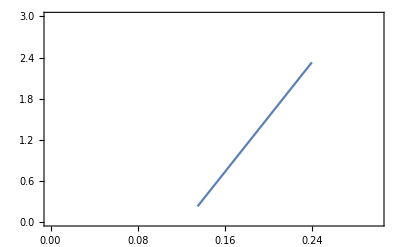

```mathematica
ListPlot[{{0.13491282073130292,0.2268},{0.14355205002196655,0.4},{0.14854010814903354,0.5},{0.22336541291766115,2.0},{0.2398280955445679,2.33}},Joined->True,plotsci,PlotRange->{{0.,0.3},{0,3.0}}]
```

Gradient descent now to find maximum

```mathematica
plotsci
```

{Frame→True,FrameStyle→Thickness[0.002],LabelStyle→Directive[FontSize→14,GrayLevel[0]]}

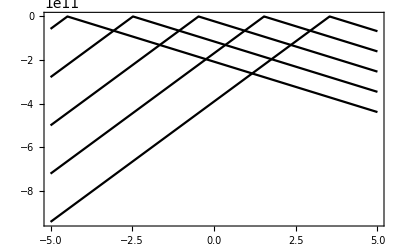

```mathematica
pp=Plot[{mineig[4,-0.1,y],mineig[4,0.0,y],mineig[4,0.1,y],mineig[4,0.2,y],mineig[4,0.3,y]},{y,-5,5},PlotStyle->Black,Axes->True,Frame->True,FrameStyle->Thickness[0.002],LabelStyle->Directive[FontSize->14,GrayLevel[0]],AxesOrigin-> {0,0}]
```

```mathematica
Labeled[pp,{"min λ","tr A^2B"},{Left,Bottom},labelsci]
```

-Graphics-min λtr A^2B

```mathematica
NMaximize[mineig[4,0.16,y],y,AccuracyGoal->3,PrecisionGoal->3]
```

{-69.3648,{y→0.729744}}

```mathematica
mineig[4,0.15,0.5292676]
```

-28.4067

```mathematica
RegionPlot[mineig[3,x,y]>-10^3,{x,0.134,0.1384},{y,0.29,0.296}]
```

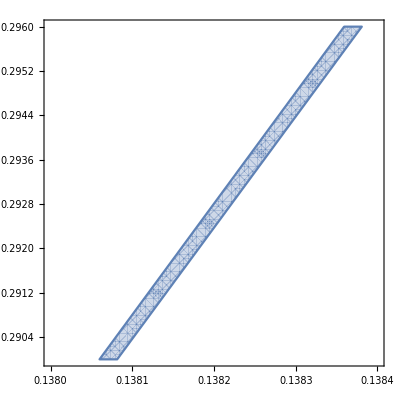

```mathematica
RegionPlot[mineig[3,x,y]>-10^3,{x,0.138,0.1384},{y,0.29,0.296}]
```

```mathematica
0.138235-13.823
```

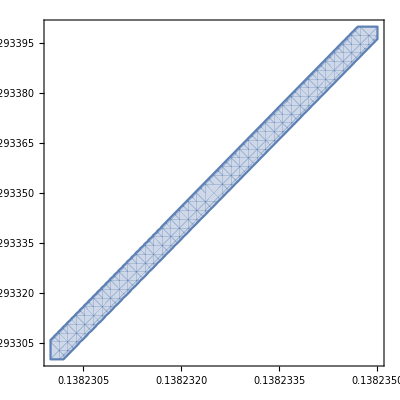

```mathematica
RegionPlot[mineig[3,x,y]>-20,{x,0.13823,0.138235},{y,0.29330,0.2934}]
```

```mathematica
dat=Flatten[Table[{x,y,mineig[3,x,y]},{x,0.137,0.139,0.0005},{y,0.28,0.3,0.005}],1];
```

```mathematica
dat
```

{{0.137,0.28,-107676.},{0.137,0.285,-155088.},{0.137,0.29,-202499.},{0.137,0.295,-249911.},{0.137,0.3,-297323.},{0.1375,0.28,-12624.3},{0.1375,0.285,-60036.},{0.1375,0.29,-107448.},{0.1375,0.295,-154859.},{0.1375,0.3,-202271.},{0.138,0.28,-26609.8},{0.138,0.285,-11301.8},{0.138,0.29,-12396.2},{0.138,0.295,-59807.8},{0.138,0.3,-107219.},{0.1385,0.28,-57299.4},{0.1385,0.285,-41991.4},{0.1385,0.29,-26683.4},{0.1385,0.295,-11375.4},{0.1385,0.3,-12168.},{0.139,0.28,-87989.},{0.139,0.285,-72681.},{0.139,0.29,-57373.},{0.139,0.295,-42065.},{0.139,0.3,-26757.}}

```mathematica
DeleteCases[dat,p_/;p[[3]]<-10^4]
```

{}

```mathematica
RegionPlot[mineig[3,x,y]>-10^4,{x,0.13,0.15},{y,0.3,0.4},PlotPoints->60]
```

$Aborted

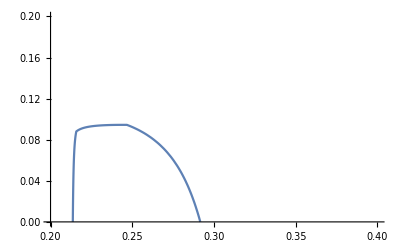

```mathematica
Plot[Min@Eigenvalues[posm[4]*1./.sol],{Subscript[e, {1}],0.20,0.4},PlotRange->{0,0.2}]
```

```mathematica
Plot[Min@Eigenvalues[posm[3]/.sol],{Subscript[e, {1}],-0.4,0.1}]
```

$Aborted

Here we see that no values are allowed at values above g=1/12

```mathematica
sol=Solve[loopAll[8]/.{g2->g1}/.{g1->1/10}];
```

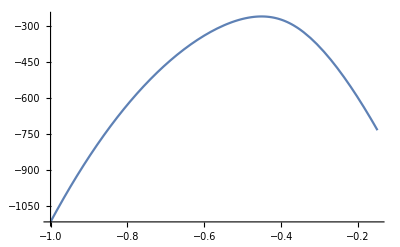

```mathematica
Plot[Min@Eigenvalues[posm[4]/.sol],{Subscript[e, {1}],-1,-0.15}]
```

#### some analytic stuff

```mathematica
vv=1/2 x^2+1/2 y^2+g 1/3(x^3+y^3)+h(x^2 y + y x^2);
```

```mathematica
g=0.07;h=0.05;
```

```mathematica
solvv=Simplify[(Solve[{D[vv,x]==0,D[vv,y]==0},{x,y}])]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→-14.2857},{x→0.,y→0.},{x→5.97599,y→-7.0916},{x→-5.00892,y→-3.24688}}

```mathematica
Eigenvalues[{{D[vv,{x,2}],D[vv,{x,1},{y,1}]},{D[vv,{x,1},{y,1}],D[vv,{y,2}]}}]/.solvv/.{h->-2.0}
```

{{-1.85714,-1.},{1.,1.},{-1.,1.4255},{-1.,1.19481}}

```mathematica
Eigenvalues[{{1,4},{4,1}}]
```

{5,-3}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{13.7299,{0.236334,{x→0.140565,y→0.340111}}}

### general g and h

```mathematica
Do[
s007cl=sols[8,0.07,0.051];
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k]/.{s007cl}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
Timing[xpyp=NMaximize[mineig[4,x,y],{x,y},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->2000]
]]
```

$Aborted

```mathematica
Timing[solutionsdat=Reap[Do[scl=sols[8,g,h];Sow[{g,h,scl}],{g,-0.16,0.16,0.01},{h,0.,0.15,0.005}]]; ]
```

{15819.1,Null}

```mathematica
DumpSave["solutionsdat.mx",solutionsdat];
```

```mathematica
<<solutionsdat.mx
sdat=solutionsdat[[2,1]];
```

```mathematica
sVeryClose=sols[8,3/10,31/100];
```

```mathematica
sol00=sVeryClose;
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k,1.0]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];(** Here we choose λ to be some small num **)
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
```

```mathematica
posmsol[4,1.0,1.0];
```

```mathematica
NMaximize[mineig[3,x,y],{x,y},PrecisionGoal->30,AccuracyGoal->30,MaxIterations->1000]
```

{-2.65928,{x→-0.190312,y→645.435}}

solution 597 (0.03,0.035)

```mathematica
sdat[[597,;;2]]
```

{0.03,0.035}

```mathematica
sol00=sdat[[597,3]];
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
```

```mathematica
NMaximize[mineig[4,x,y],{x,y}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.133055,{x→0.0828977,y→1.88987}}

```mathematica
NMaximize[mineig[4,0.134,y],{y}]
```

{0.00492788,{y→3.79687}}

```mathematica
NMaximize[mineig[4,0.13,y],{y}]
```

{0.0299544,{y→4.48681}}

```mathematica
NMaximize[mineig[4,0.068,y],{y}]
```

{0.131054,{y→1.61499}}

```mathematica
NMaximize[mineig[4,0.067,y],{y}]
```

{-9725.24,{y→5.5499}}

Here we try exactly (0.3,0.3) we need to write some special code

```mathematica
sdat[[596,;;2]]
```

{0.03,0.03}

```mathematica
sol00=sdat[[596,3]];
posmsolSp[k_Integer,x_?NumericQ]:=(posm[k,1.0]/.{sol00}/.{Subscript[e, {1}]->x})[[1,1]];
mineigSp[k_,x_?NumericQ]:=Min[Eigenvalues@posmsolSp[k,x]];
```

```mathematica
NMaximize[mineigSp[4,x],{x}]
```

$Aborted

```mathematica
mineigSp[4,0.062]
```

0.116286

```mathematica
mineigSp[4,0.121]
```

0.0040957

```mathematica
(Subscript[e, {1,1,2}]/.{sol00})/.{Subscript[e, {1}]->0.121}
```

{{4.17561}}

```mathematica
mineigdat=Table[
sol00=sdat[[i,3]];
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
Print[i];
If[sdat[[i,1]]==sdat[[i,2]]||sdat[[i,2]]==0 ,
{sdat[[i,1]],sdat[[i,2]],0},
{sdat[[i,1]],sdat[[i,2]],
NMaximize[mineig[4,x,y],{x,y},AccuracyGoal->15,PrecisionGoal->15,MaxIterations->5000]}]
,{i,1,Length@sdat}];//Timing
```

{50134.,Null}

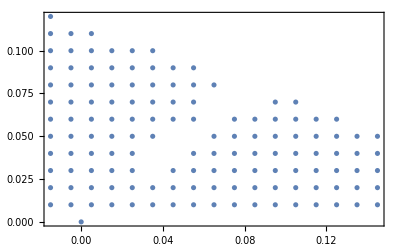

```mathematica
ListPlot[{validpts},plotsci,PlotRange->Full]
```

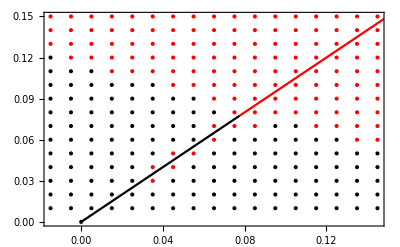
-Graphics-gh

```mathematica
Labeled[Show[ListPlot[{validpts,invalidpts},plotsci,PlotRange->Full,PlotStyle->{Black,Red,Darker@Green}],Plot[g,{g,0.07755040492517497,2},PlotStyle->Red],Plot[g,{g,0,0.07755040492517497},PlotStyle->Black]],{"g","h"},{Bottom,Left},labelsci]
```

```mathematica
pmin=If[Length[#[[3]]]==0,{0,0},If[#[[3,1]]>0,#[[;;2]],{0,0}] ]&;
```

```mathematica
pmininv=If[Length[#[[3]]]==0,{0,0},If[#[[3,1]]<0,#[[;;2]],{0,0}] ]&;
```

```mathematica
pminerr=If[Length[#[[3]]]==0,#[[;;2]],{0,0} ]&;
```

```mathematica
validpts=DeleteDuplicates[pmin/@mineigdat];
invalidpts=DeleteCases[DeleteDuplicates[pmininv/@mineigdat],{0,0}];
errpts=DeleteCases[DeleteDuplicates[pminerr/@mineigdat],{0,0}];
```

```mathematica
Evaluate[mineigdat[[2,3]]==0]
```

{0.148653,{x→-0.00618668,y→25.7055}}==0

```mathematica
DumpSave["mineigdat.mx",mineigdat];
```

```mathematica
Clear[mineigdat]
```

```mathematica
<<"mineigdat.mx"
```

```mathematica
sol0=solutionsdat[[2,1,3,3]];
```

```mathematica
posmsol[k_Integer,x_?NumericQ,y_?NumericQ]:=(posm[k]/.{sol0}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
mineig[k_,x_?NumericQ,y_?NumericQ]:=Min[Eigenvalues@posmsol[k,x,y]];
Timing[xpyp=NMaximize[mineig[4,x,y],{x,y},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->2000]]
```

{50.8628,{0.138163,{x→0.0270795,y→7.56524}}}

```mathematica
sol0=solutionsdat[[2,1,9,;;2]]
```

{0.,0.15}

```mathematica
mineigx[k_Integer,x_?NumericQ,y_?NumericQ]:=(mineig[k,x+10^-12,y]-mineig[k,x-10^-12,y])*10^12;
mineigy[k_Integer,x_?NumericQ,y_?NumericQ]:=(mineig[k,x,y+10^-12]-mineig[k,x,y-10^-12])*10^12
```

```mathematica
Timing[xpyp=NMaximize[mineig[4,x,y],{x,y},AccuracyGoal->30,PrecisionGoal->30,MaxIterations->2000]
]
```

{40.2216,{-1520.9,{x→0.1493,y→0.126049}}}

```mathematica
yp=0.5;
Timing[xpyp=FindMaximum[mineig[4,x,yp],{x,-1,1},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->1000,Gradient-> {mineigx[4,x,yp]}]
]
```

FindMaximum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{6.89142,{-2.89377×10^6,{x→0.180501}}}

### better approach

Here we would like to try a different method that does not use Maximize, and does less eigenvalue computation.
Instead we would like to compute the determinant (easy) of the matrix, and find its zero curves.

Notice that there is something curious happening at g= -h/3.

```mathematica
Factor[(a^3+b^3-a^2b-a b^2)]
```

(a-b)^2 (a+b)

```mathematica
Expand[(a+b)^2 (a-b)]
```

a^3+a^2 b-a b^2-b^3

```mathematica
solqq=sols[8,-3/20,1/20]
```

Here we consider some random point at g=-h.

```mathematica
sol00=sols[10,-3/20,3/20];
DumpSave["sol00.mx",sol00];
```

```mathematica
sol18=sols[10,-3/18,3/18];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
DumpSave["sol18.mx",sol18];
```

```mathematica
sol16=sols[10,-3/16,3/16];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
DumpSave["sol16.mx",sol16];
```

```mathematica
<<"sol00.mx"
innermat00[k_Integer,x_,y_]:=(posmlite[k]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
xBigMat[k_Integer,x_,y_]:=(posm[k]/.{sol00}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
NMaximize[Min[Eigenvalues[xBigMat[3,x,y]]],{x,y}]//Timing
```

{27.5246,{0.546792,{x→-3.93762×10^-11,y→1.20984}}}

```mathematica
Dimensions@xBigMat[6,0,0.7]
```

{126,126}

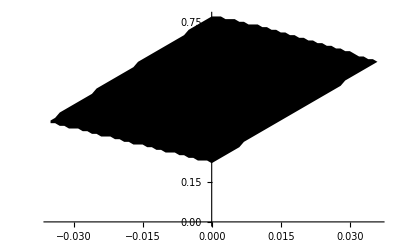

```mathematica
pdat=#[[;;2]]&/@DeleteCases[rplot,p_/;p[[3]]<0];
lowdat=MinimalBy[#,Last][[1]]&/@GatherBy[pdat,First];
updat=MaximalBy[#,Last][[1]]&/@GatherBy[pdat,First];tBigdat=ListPlot[{lowdat,updat},Joined->True,PlotStyle->Opacity[0],Filling->{1->{2}},FillingStyle->Black,InterpolationOrder->1]
```

```mathematica
rplot=Parallelize[Outer[{#1,#2,me[#1,#2]}&,Range[-0.05,0.05,0.001],Range[0.18,0.8,0.01]]];//Timing
rplot=Flatten[rplot,1];
```

{36.4543,Null}

```mathematica
me[t1_,t2_]:=Min[Eigenvalues[xBigMat[5,t1,t2]]]
```

```mathematica
bSol=y/.Solve[Det[bigmat[3,x,y]]==0,y];
```

```mathematica
N[Min@Eigenvalues[bigmat[2,0.1,0.2]],3]
```

-5.92777

```mathematica
bSol/.{x->0.}
```

```mathematica
r3=RegionPlot[Min@Eigenvalues[bigmat[3,x,y]]>0,{x,-0.5,1.0},{y,0,11}, PlotStyle->Directive[Opacity[0.15],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

{19.3954,Null}

```mathematica
r4=RegionPlot[Min@Eigenvalues[bigmat[4,x,y]]>0,{x,-0.2,0.4},{y,0,5} ,PlotStyle->Directive[Opacity[0.25],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

{35.8406,Null}

```mathematica
r5=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.2,0.4},{y,0,2} ,PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None];//Timing
```

{470.117,Null}

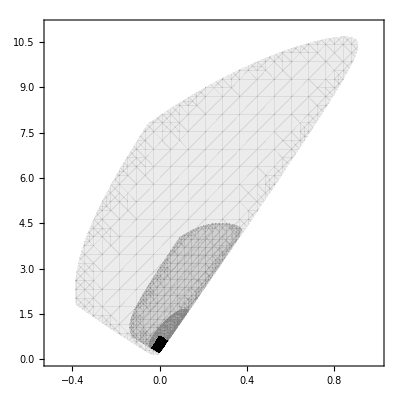
-Graphics-tr A^2Btr A

```mathematica
Labeled[Show[r3,r4,r5,tBigdat,plotsci],{"tr A^2B","tr A"},{Left,Bottom},labelsci]
```

#### using only single matrix correlators

```mathematica
sol00=sols[10,-3/20,3/20];
DumpSave["sol00.mx",sol00];
```

```mathematica
ysol=y/.Solve[Det@innermat00[6,x,y]==0,y];
res=1/200;
ys1=Table[{x,1.*ysol[[2]]},{x,-.7,1.5,res}];
ys2=Table[{x,1.*ysol[[3]]},{x,-.7,1.5,res}];
```

```mathematica
ysol=y/.Solve[Det@innermat00[8,x,y]==0,y];
res=1/200;
ys18=Table[{x,1.*ysol[[3]]},{x,-.36,.5,res}];
ys28=Table[{x,1.*ysol[[4]]},{x,-.36,.5,res}];
```

```mathematica
ysol=y/.Solve[Det@innermat00[10,x,y]==0,y];
res=1/300;
```

```mathematica
ys110=Table[{x,1.*ysol[[3]]},{x,-.0,.2,res}];
ys210=Table[{x,1.*ysol[[4]]},{x,-.0,.2,res}];
```

```mathematica
ys210;
```

```mathematica
r003=RegionPlot[Min@Eigenvalues[innermat00[6,x,y]]>0,{x,-0.7,1.5},{y,0,16} ,PlotStyle->Directive[Opacity[0.15],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

{6.44058,Null}

```mathematica
r004=RegionPlot[Min@Eigenvalues[innermat00[8,x,y]]>0,{x,-0.2,0.6},{y,0,10} ,PlotStyle->Directive[Opacity[0.25],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

{7.93156,Null}

```mathematica
r005=RegionPlot[Min@Eigenvalues[innermat00[10,x,y]]>0,{x,-0.2,0.4},{y,0,3} ,PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

{10.0314,Null}

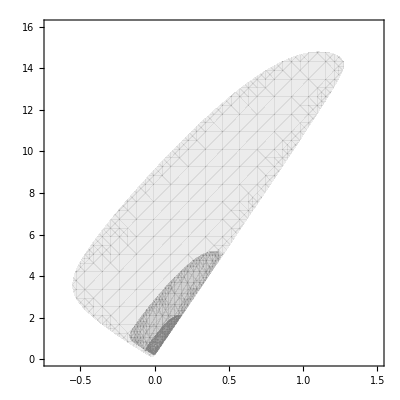
-Graphics-tr A^2Btr A

```mathematica
Labeled[Show[r003,r004,r005,Graphics[{Opacity[0],EdgeForm[Dashed],Rectangle[{-0.5,0},{1,11}]}],plotsci],{"tr A^2B","tr A"},{Left,Bottom},labelsci]
```

### passing the critical pt

#### Attempt 2

```mathematica
-3/16.
```

-0.1875

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol18}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
sol17=sols[10,-185/1000,185/1000];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
xBigMat[k_Integer,x_,y_]:=(posm[k]/.{sol17}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
me[t1_,t2_]:=Min[Eigenvalues[xBigMat[5,t1,t2]]]
```

```mathematica
rplot2=Parallelize[Outer[{#1,#2,me[#1,#2]}&,Range[-0.15,0.1,0.005],Range[0.3,1.5,0.05]]];//Timing
rplot2=Flatten[rplot2,1];
```

{7.50872,Null}

```mathematica
FindMaximum[me[0,y],{y,0.49}]
```

$Aborted

```mathematica
me[0,0.50]
```

-0.0407298

```mathematica
MaximalBy[rplot2,Last]
```

{{1.38778×10^-17,0.5,-0.0407298}}

```mathematica
pdat=#[[;;2]]&/@DeleteCases[rplot2,p_/;p[[3]]<0];
lowdat=MinimalBy[#,Last][[1]]&/@GatherBy[pdat,First];
updat=MaximalBy[#,Last][[1]]&/@GatherBy[pdat,First];tBigdat=ListPlot[{lowdat,updat},Joined->True,PlotStyle->Opacity[0],Filling->{1->{2}},FillingStyle->Black,InterpolationOrder->1]
```

-Graphics-

```mathematica
FindMaximum[me[0,y],{y,0}]
```

$Aborted

```mathematica
FindMaximum[Min@Eigenvalues[bigmat[5,x,y]],{y,0.9},{x,0}]
```

{-0.150503,{y→0.619053,x→0.0136977}}

```mathematica
rg18=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.1,0.2},{y,0,1.5} ,PlotStyle->Directive[Opacity[0.3],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];//Timing
```

$Aborted

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol16}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
rg16=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.1,0.2},{y,0,1.5} ,PlotStyle->Directive[Opacity[0.3],Lighter@Red] , BoundaryStyle->None];//Timing
```

{451.31,Null}

```mathematica
FindMaximum[Min@Eigenvalues[bigmat[5,0,y]],{y,0.9}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.171545,{y→0.547916}}

### finding the critical pt on the g=-h line

```mathematica
sol00=sols[10,-3/20,3/20];
```

```mathematica
<<sol00.mx
```

```mathematica
sol16=sols[10,-3/16,3/16];
```

```mathematica
<<sol16.mx
```

```mathematica
sol18=sols[10,-3/18,3/18];
```

```mathematica
<<sol18.mx
```

```mathematica
sol18=sols[10,-3/18,3/18];
```

```mathematica
sol17=sols[10,-3/17,3/17];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
DumpSave["sol17.mx",sol17];
```

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol18}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
r5g18=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.2,0.4},{y,0,2} ,PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None,PlotPoints->100];//Timing
```

{656.336,Null}

```mathematica
hv
```

```mathematica
r5g18
```

-Graphics-

previous timing was 421 sec w/out

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol20}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
r5g20=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.2,0.4},{y,0,2} ,PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None,PlotPoints->100];//Timing
```

ReplaceAll::reps: {sol20} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues::matsq: Argument {e_{1,1},e_{1,1,1},e_{1,1,1,1},e_{1,1,1,1,1},e_{1,1,1,1,1,1},e_{1,2},y,e_{1,1,1,2},e_{1,1,1,1,2},e_{1,1,1,1,1,2}} at position 1 is not a non-empty square matrix.

ReplaceAll::reps: {sol20} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Eigenvalues::matsq: Argument {e_{1,1},e_{1,1,1},e_{1,1,1,1},e_{1,1,1,1,1},e_{1,1,1,1,1,1},e_{1,2},y,e_{1,1,1,2},e_{1,1,1,1,2},e_{1,1,1,1,1,2}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {e_{1,1},e_{1,1,1},e_{1,1,1,1},e_{1,1,1,1,1},e_{1,1,1,1,1,1},e_{1,2},0.0000202222,e_{1,1,1,2},e_{1,1,1,1,2},e_{1,1,1,1,1,2}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

{93.0008,Null}

```mathematica
bigmat[k_Integer,x_,y_]:=(posMed[k]/.{sol16}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
```

```mathematica
r5g16=RegionPlot[Min@Eigenvalues[bigmat[5,x,y]]>0,{x,-0.2,0.4},{y,0,2} ,PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None];//Timing
```

{427.365,Null}

```mathematica
r5g16
```

-Graphics-

```mathematica
1->{{2},{LightRed}},3->{{4},{Darker[LightYellow,0.01]}},5->{{6},Lighter[Green,0.7]} ,7->{{8},Lighter[Blue,0.7]},9->{{10},Gray}
```

```mathematica
rt2=RegionPlot[(x-0.1)^2+y^2<0.5,{x,-2,2},{y,-2,2},PlotStyle->Directive[Opacity[0.3],LightRed] ,BoundaryStyle->Black];
```

```mathematica
rt1=RegionPlot[x^2+y^2<1,{x,-2,2},{y,-2,2}];
```

```mathematica
rt2=RegionPlot[(x-1)^2+y^2<0.9,{x,-2,2},{y,-2,2},PlotStyle->Directive[Opacity[1]] ];
```

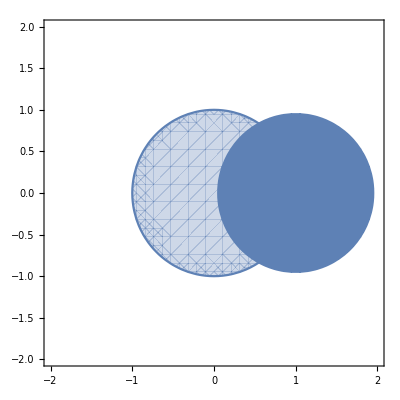

```mathematica
Show[rt2,rt1]
```

#### attempt 1

Here we consider some random point at g=-h. we now push it to stronger coupling

```mathematica
sol16=sols[8,-3/16,3/16];
innermat16[k_Integer,x_,y_]:=(posmlite[k]/.{sol16}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
ysol16=y/.Solve[Det@innermat16[8,x,y]==0,y];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
y16[k_]:=Table[{x,1.*ysol16[[k]]},{x,-.1,0.25,res}];
```

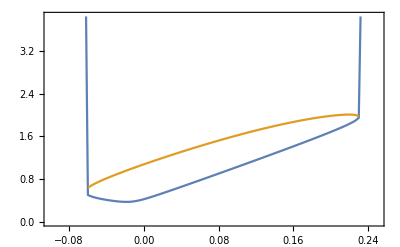

```mathematica
ListPlot[{y16[3],y16[4]},Joined->True,Evaluate@plotsci]
```

```mathematica
innermat18[k_Integer,x_,y_]:=(posmlite[k]/.{sol18}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
ysol18=y/.Solve[Det@innermat18[8,x,y]==0,y];
y18[k_]:=Table[{x,1.*ysol18[[k]]},{x,-.2,0.4,res}];
```

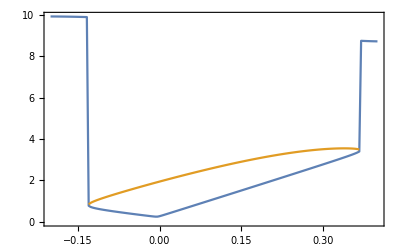

```mathematica
ListPlot[{y18[3],y18[4]},Joined->True,Evaluate@plotsci]
```

```mathematica
sol31=sols[8,-6/31,6/31];
innermat31[k_Integer,x_,y_]:=(posmlite[k]/.{sol31}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
ysol31=y/.Solve[Det@innermat31[8,x,y]==0,y];
res=1/500;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
y31[k_]:=Table[{x,1.*ysol31[[k]]},{x,-0.1,0.2,res}];
```

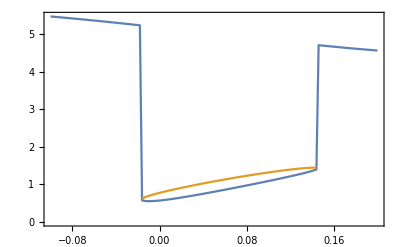

```mathematica
ListPlot[{y31[3],y31[4]},Joined->True,Evaluate@plotsci]
```

```mathematica
sol195=sols[8,-195/1000,195/1000];
innermat195[k_Integer,x_,y_]:=(posmlite[k]/.{sol195}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
ysol195=y/.Solve[Det@innermat195[8,x,y]==0,y];
res=1/500;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
y195[k_]:=Table[{x,1.*ysol195[[k]]},{x,0,0.1,res}];
```

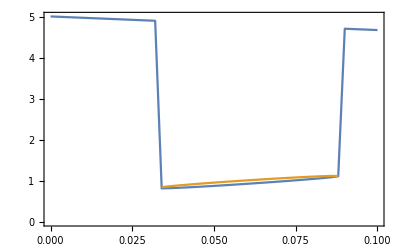

```mathematica
ListPlot[{y195[3],y195[4]},Joined->True,Evaluate@plotsci]
```

```mathematica
{3/20,3/18,3/16,6/31,0.195}*1.
```

{0.15,0.166667,0.1875,0.193548,0.195}

```mathematica
ff=
Filling->{
1->{{2},{LightRed}},3->{{4},{Darker[LightYellow,0.01]}},5->{{6},Lighter[Green,0.7]} ,7->{{8},Lighter[Blue,0.7]},9->{{10},Gray}};
```

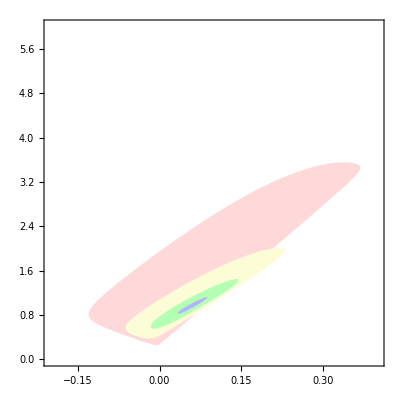
-Graphics-tr A^2Btr A

```mathematica
Labeled[Show[ListPlot[{y18[3],y18[4],y16[3],y16[4],y31[3],y31[4],y195[3],y195[4]},Joined->True,PlotRange->{Automatic,{0,6}},PlotStyle->Opacity[0],
ff
],Evaluate@plotsci,AspectRatio->1],{"tr A^2B","tr A"},{Left,Bottom},labelsci]
```

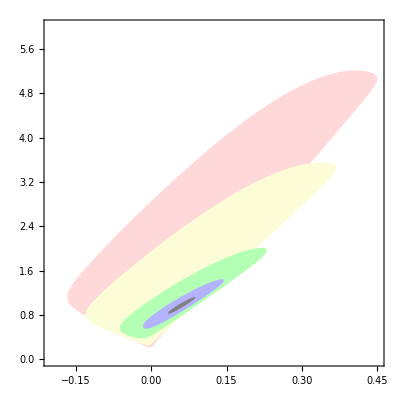
-Graphics-tr A^2Btr A

```mathematica
Labeled[Show[ListPlot[{y00[3],y00[4],y18[3],y18[4],y16[3],y16[4],y31[3],y31[4],y195[3],y195[4]},Joined->True,PlotRange->{Automatic,{0,6}},PlotStyle->Opacity[0],
ff
],Evaluate@plotsci,AspectRatio->1],{"tr A^2B","tr A"},{Left,Bottom},labelsci]
```

### trying to find the critical surface

```mathematica
<<solutionsdat.mx
sdat=solutionsdat[[2,1]];
```

```mathematica
sol7=sols[8,1/20,1/20];
```

```mathematica
innermat7[k_Integer,x_]:=(posmlite[k]/.{sol7}/.{Subscript[e, {1}]->x})[[1,1]];
```

```mathematica
Subscript[e, {1,1,2}]/.sol7/.{Subscript[e, {1}]->1/2}
```

{39/4}

```mathematica
Simplify[0.01020408163265306 (-175.+1201. Subscript[e, {1}])]
```

-1.78571+12.2551 e_{1}

```mathematica
0.01020408163265306 (-175.+1201. Subscript[e, {1}])/.{Subscript[e, {1}]->0.33}
```

2.25847

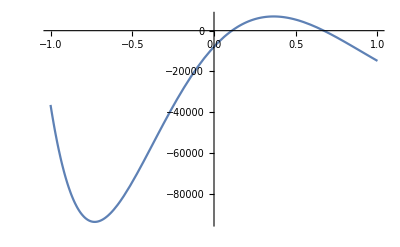

```mathematica
Plot[Det@innermat7[8,x],{x,-1,1}]
```

```mathematica
sol31=sols[8,1/20,1/20-1/1000];
```

```mathematica
innermat31[6,x,y][[3,3]]//MatrixForm
```

5.002×10^-18 (4.996×10^26-4.89659×10^27 x+9.994×10^20 x^2+1.998×10^26 y)

```mathematica
innermat31[k_Integer,x_,y_]:=(posmlite[k]/.{sol31}/.{Subscript[e, {1}]->x,Subscript[e, {1,1,2}]->y})[[1,1]];
ysol31=y/.Solve[Det@innermat31[8,x,y]==0,y];
res=1/500;
```

```mathematica
1.innermat7[6,x]/.{x->1/2}//MatrixForm
```

(1. | 0.5 | 3. | 10.75
0.5 | 3. | 10.75 | 53.25
3. | 10.75 | 53.25 | 253.75
10.75 | 53.25 | 253.75 | 1243.44)

```mathematica
1.innermat31[6,x,y]/.{x->1/2,y->39/4}//MatrixForm
```

(1. | 0.5 | 3.03669 | 12.0687
0.5 | 3.03669 | 12.0687 | -30967.8
3.03669 | 12.0687 | -30967.8 | -7.91983×10^7
12.0687 | -30967.8 | -7.91983×10^7 | 1.44095×10^12)

```mathematica
FindMaximum[Eigenvalues[innermat31[6,x,y]][[1]],{x,y}]
```

{-7054.34,{x→0.144073,y→1.03483}}

```mathematica
FindMaximum[Eigenvalues[innermat31[6,x,y]][[1]],{x,y}]
```

{0.573097,{x→0.14191,y→1.03397}}

```mathematica
-1.7857142857142856+12.255102040816325 Subscript[e, {1}]/.{Subscript[e, {1}]->0.202}
```

0.689816

```mathematica
innermat31[8,0.20260838931290748,0.69]//Eigenvalues
```

{1.15517×10^11,-3.37648×10^8,6.63212,0.965492,0.60352}

```mathematica
y31[k_]:=Table[{x,1.*ysol31[[k]]},{x,-0.1,0.1,res}];
```

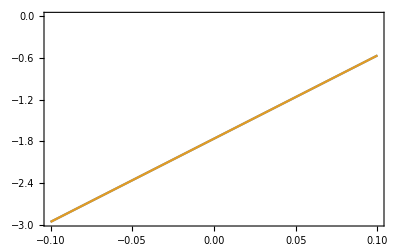

```mathematica
ListPlot[{y31[3],y31[4]},Joined->True,Evaluate@plotsci]
```

```mathematica
Eigenvalues[N[innermat31[8,-20,3]] ,-1]
```

{6.20914}

```mathematica
y31[k_]:=Table[{x,1.*ysol31[[k]]},{x,-5,1,res}];
```

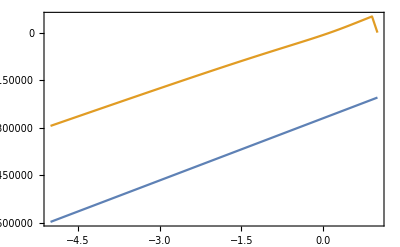

WolframAlphaQueryResults

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
Sort[necklaceElements[{A, B, C}]]

<>$Failed<>
{{A, B, C}, {B, C, A}, {C, A, B}}

<>$Failed<>
{"NestedList$DisplayAs", "NestedList$Dimensions", "NestedList$Transpose", "NestedList$Flatten", "NestedList$ReverseSublists", "NestedList$Rotate2DArray", "NestedList$Reflect2DArray"}



<>$Failed<>


[12.0.0.0 (6206964, 2019040701); MacOSX-x86-64; 3027-0113-WHJEJG; paclet 12.1.128]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

```mathematica
ListPlot[y31/@{1,2},Joined->True,Evaluate@plotsci]
```